```mathematica
d[n_,0,a_]:=1
d[n_,1,a_]:=n-a+1
d[n_,k_,a_]:=Sum[Binomial[k,j]d[Floor[n/(m^j)],k-j,m+1],{j,1,k},{m,a,n^(1/k)}]

D32Unrolled[ n_ ] := -1 + Floor[ n^(1/3)]^3 + 3 Sum[ Floor[ n/(m^2)] - Floor[ Floor[n/m]^(1/2)]^2 + 2 Sum[ Floor[Floor[n/m]/j],{j,m+1,Floor[Floor[n/m]^(1/2)]}], {m,2,Floor[n^(1/3)]}]

D22Unrolled[ n_ ] := 1 - Floor[ n^(1/2)]^2 + 2 Sum [ Floor[ n/m],{m,2,Floor[n^(1/2)]}]
d0[n_,a_Integer] := 1
d1[n_, a_Integer] := n-a+1
d2a[n_, a_Integer] := Sum[ Binomial[ 2,2 ]d0[Floor[n/(m^2)],m+1] , {m,a,Floor[n^(1/2)]}]+
Sum[Binomial[ 2,1 ]d1[Floor[n/(m^1)],m+1], {m,a,Floor[n^(1/2)]}]
d2[n_, a_Integer] := 1 - 2 a + a^2 -Floor[ n^(1/2)]^2 + 2 Sum [ Floor[ n/m],{m,a,Floor[n^(1/2)]}]
d2[0,a_Integer] := 0
d3a[n_, a_Integer] := Sum[ Binomial[ 3,3 ]d0[Floor[n/(m^3)],m+1] , {m,a,Floor[n^(1/3)]}]+
Sum[Binomial[ 3,2 ]d1[Floor[n/(m^2)],m+1], {m,a,Floor[n^(1/3)]}]+
Sum[Binomial[ 3,1 ]d2a[Floor[n/(m^1)],m+1], {m,a,Floor[n^(1/3)]}]
```

```mathematica
d3b[n_, a_Integer] := Sum[1 , {m,a,Floor[n^(1/3)]}]+
Sum[3 ( Floor[n/(m^2)] - m), {m,a,Floor[n^(1/3)]}]+
Sum[3 d2[Floor[n/m],m+1], {m,a,Floor[n^(1/3)]}]
```

```mathematica
d3b[n,2]
```

-1+Floor[n^(1/3)]+∑_(m=2)^Floor[n^(1/3)] 3 d2[Floor[n/m],1+m]+∑_(m=2)^Floor[n^(1/3)] 3 (-m+Floor[n/m^2])

```mathematica
d[100,4,2]
```

184

```mathematica
d2e[n_, a_Integer] := (1-a)^2 -Floor[ n^(1/2)]^2 + 2 Sum [ Floor[ n/m],{m,a,Floor[n^(1/2)]}]
d2e[123210,4]
```

1011514

```mathematica
d[123210,2,4]
```

1011514

```mathematica
dd3[n_, a_ ] := Sum[ 3(Floor[n/(s^2)]-s) + 1 +3(1-2(s+1)+(s+1)^2 - Floor[Floor[n/s]^(1/2)]^2 + 2 Sum[ Floor[n/m/s],{m,s+1,Floor[Floor[n/s]^(1/2)]}]),{s,a,Floor[n^(1/3)]}]
```

```mathematica
dd3[100,3]
```

71

```mathematica
d[100,3,3]
```

71

```mathematica
d3c[100,2]
```

324

```mathematica
d3c[n_, a_Integer] :=
Sum[1+3 ( Floor[n/(m^2)] - m), {m,a,Floor[n^(1/3)]}]+
Sum[3 d2[Floor[n/m],m+1], {m,a,Floor[n^(1/3)]}]
```

```mathematica
dd3a[n_, a_ ] := Sum[ 3(Floor[n/(s^2)]-s) + 1 +3(1-2(s+1)+(s+1)^2 - Floor[Floor[n/s]^(1/2)]^2 + 2 Sum[ Floor[n/m/s],{m,s+1,Floor[Floor[n/s]^(1/2)]}]),{s,a,Floor[n^(1/3)]}]
```

```mathematica
dd3a[200,2]
```

1027

```mathematica
d[200,3,2]
```

1027

```mathematica
Expand[FullSimplify[3(Floor[n/(s^2)]-s) + 1 +3(1-2(s+1)+(s+1)^2 - Floor[Floor[n/s]^(1/2)]^2)]]
```

1-3 s+3 s^2+3 Floor[n/s^2]-3 Floor[√Floor[n/s]]^2

```mathematica
dd3b[n_, a_ ] := Sum[ 1-3 s+3 s^2+3 Floor[n/s^2]-3 Floor[√Floor[n/s]]^2 + 6 Sum[ Floor[n/m/s],{m,s+1,Floor[Floor[n/s]^(1/2)]}],{s,a,Floor[n^(1/3)]}]
```

```mathematica
dd3b[200,2]
```

1027

```mathematica
dd3c[n_, a_ ] := Sum[ 1-3 s+3 s^2,{s,a,Floor[n^(1/3)]}]+Sum[3 Floor[n/s^2]-3 Floor[√Floor[n/s]]^2 + 6 Sum[ Floor[n/m/s],{m,s+1,Floor[Floor[n/s]^(1/2)]}],{s,a,Floor[n^(1/3)]}]
```

```mathematica
dd3c[200,2]
```

1027

```mathematica
Expand[FullSimplify[Sum[1-3 s+3 s^2,{s,a,Floor[n^(1/3)]}]]]
```

1-3 a+3 a^2-a^3+Floor[n^(1/3)]^3

```mathematica
dd3d[n_, a_ ] := 1-3 a+3 a^2-a^3+Floor[n^(1/3)]^3+Sum[3 Floor[n/s^2]-3 Floor[√Floor[n/s]]^2 + 6 Sum[ Floor[n/m/s],{m,s+1,Floor[Floor[n/s]^(1/2)]}],{s,a,Floor[n^(1/3)]}]
```

```mathematica
dd3d[300,3]
```

709

```mathematica
dd3e[n_, a_ ] := (1-a)^3+Floor[n^(1/3)]^3+Sum[3 Floor[n/s^2]-3 Floor[√Floor[n/s]]^2 + 6 Sum[ Floor[n/m/s],{m,s+1,Floor[Floor[n/s]^(1/2)]}],{s,a,Floor[n^(1/3)]}]
```

```mathematica
dd3e[300,3]
```

709

```mathematica
d[300,3,3]
```

709

```mathematica
d4[x_, b_ ] := Sum[ d[Floor[x/(u^4)],0,u+1] + 4 d[Floor[x/(u^3)],1,u+1]+ 6 d[Floor[x/(u^2)],2,u+1]+4 d[Floor[x/(u^1)],3,u+1],{u, b, Floor[x^(1/4)]}]
```

```mathematica
d4[100,2]
```

184

```mathematica
d[10000,4,3]
```

171994

```mathematica
Floor[(100)^(1/4)]
```

3

```mathematica
d4a[x_, b_ ] := Sum[ 1 + 4 (Floor[x/(u^3)]-u)+ 6 d[Floor[x/(u^2)],2,u+1]+4 d[Floor[x/(u^1)],3,u+1],{u, b, Floor[x^(1/4)]}]
```

```mathematica
d4a[10000,3]
```

171994

```mathematica
d4b[x_, b_ ] := Sum[ 1 + 4 (Floor[x/(u^3)]-u)

+ 6( 1 - 2 (u+1) + (u+1)^2 -Floor[ Floor[x/(u^2)]^(1/2)]^2 + 2 Sum [ Floor[ Floor[x/(u^2)]/m],{m,(u+1),Floor[Floor[x/(u^2)]^(1/2)]}])

+4 d[Floor[x/(u^1)],3,u+1],{u, b, Floor[x^(1/4)]}]
```

```mathematica
d4b[22200,3]
```

605878

```mathematica
#a=(u+1) # n = Floor[x/u]
```

```mathematica
d4c[x_, b_ ] := Sum[ 1 + 4 (Floor[x/(u^3)]-u)

+ 6( 1 - 2 (u+1) + (u+1)^2 -Floor[ Floor[x/(u^2)]^(1/2)]^2 + 2 Sum [ Floor[ Floor[x/(u^2)]/m],{m,(u+1),Floor[Floor[x/(u^2)]^(1/2)]}])

+4( 1-3 (u+1)+3 (u+1)^2-(u+1)^3+Floor[Floor[x/u]^(1/3)]^3+Sum[3 Floor[Floor[x/u]/s^2]-3 Floor[√Floor[Floor[x/u]/s]]^2 + 6 Sum[ Floor[Floor[x/u]/m/s],{m,s+1,Floor[Floor[Floor[x/u]/s]^(1/2)]}],{s,(u+1),Floor[Floor[x/u]^(1/3)]}])

,{u, b, Floor[x^(1/4)]}]
```

```mathematica
d4c[22200,3]
```

605878

```mathematica
d[12200,4,4]
```

95137

```mathematica
d4d[x_, b_ ] := 
Sum[1+6( 1 - 2 (u+1) + (u+1)^2 )+4( 1-3 (u+1)+3 (u+1)^2-(u+1)^3-u),{u, b, Floor[x^(1/4)]}]+
Sum[
  4 Floor[x/(u^3)]+ 6(-Floor[ Floor[x/(u^2)]^(1/2)]^2 + 2 Sum [ Floor[ Floor[x/(u^2)]/m],{m,(u+1),Floor[Floor[x/(u^2)]^(1/2)]}])+4( Floor[Floor[x/u]^(1/3)]^3+Sum[3 Floor[Floor[x/u]/s^2]-3 Floor[√Floor[Floor[x/u]/s]]^2 + 6 Sum[ Floor[Floor[x/u]/m/s],{m,s+1,Floor[Floor[Floor[x/u]/s]^(1/2)]}],{s,(u+1),Floor[Floor[x/u]^(1/3)]}])

,{u, b, Floor[x^(1/4)]}]
```

```mathematica
d4d[12200,4]
```

95137

```mathematica
FullSimplify[Expand[Sum[1+6( 1 - 2 (u+1) + (u+1)^2 )+4( 1-3 (u+1)+3 (u+1)^2-(u+1)^3-u),{u, b, Floor[x^(1/4)]}]]]
```

(-1+b)^4-Floor[x^(1/4)]^4

```mathematica
Expand[Sum[1+6( 1 - 2 (u+1) + (u+1)^2 )+4( 1-3 (u+1)+3 (u+1)^2-(u+1)^3-u),{u, b, Floor[x^(1/4)]}]]
```

1-4 b+6 b^2-4 b^3+b^4-Floor[x^(1/4)]^4

```mathematica
d4e[x_, b_ ] := 
(-1+b)^4-Floor[x^(1/4)]^4+
Sum[
  4 Floor[x/(u^3)]+ 6(-Floor[ Floor[x/(u^2)]^(1/2)]^2 + 2 Sum [ Floor[ Floor[x/(u^2)]/m],{m,(u+1),Floor[Floor[x/(u^2)]^(1/2)]}])+4( Floor[Floor[x/u]^(1/3)]^3+Sum[3 Floor[Floor[x/u]/s^2]-3 Floor[√Floor[Floor[x/u]/s]]^2 + 6 Sum[ Floor[Floor[x/u]/m/s],{m,s+1,Floor[Floor[Floor[x/u]/s]^(1/2)]}],{s,(u+1),Floor[Floor[x/u]^(1/3)]}])

,{u, b, Floor[x^(1/4)]}]
```

```mathematica
d4e[72200,2]
```

7624011

```mathematica
d[72200,4,2]
```

7624011

```mathematica
Sum[
  4 Floor[x/(u^3)]+ 6(-Floor[ Floor[x/(u^2)]^(1/2)]^2 + 2 Sum [ Floor[ Floor[x/(u^2)]/m],{m,(u+1),Floor[Floor[x/(u^2)]^(1/2)]}])+4( Floor[Floor[x/u]^(1/3)]^3+Sum[3 Floor[Floor[x/u]/s^2]-3 Floor[√Floor[Floor[x/u]/s]]^2 + 6 Sum[ Floor[Floor[x/u]/m/s],{m,s+1,Floor[Floor[Floor[x/u]/s]^(1/2)]}],{s,(u+1),Floor[Floor[x/u]^(1/3)]}])

,{u, b, Floor[x^(1/4)]}]
```

```mathematica
d4f[x_, b_ ] := 
(-1+b)^4-Floor[x^(1/4)]^4+
Sum[ 
4 Floor[x/(u^3)]
+ 6(
-Floor[ Floor[x/(u^2)]^(1/2)]^2 
+ 2 Sum [ Floor[ Floor[x/(u^2)]/m],{m,(u+1),Floor[Floor[x/(u^2)]^(1/2)]}]
)
+4( 
Floor[Floor[x/u]^(1/3)]^3
+3 Sum[
	 Floor[Floor[x/u]/s^2]
	- Floor[√Floor[Floor[x/u]/s]]^2 
	+ 2 Sum[ Floor[Floor[x/u]/m/s],{m,s+1,Floor[Floor[Floor[x/u]/s]^(1/2)]}
],{s,(u+1),Floor[Floor[x/u]^(1/3)]}]),
{u, b, Floor[x^(1/4)]}]
```

```mathematica
d4g[72200,2]
```

7624011

```mathematica
d4g[x_, b_ ] := 
(-1+b)^4-Floor[x^(1/4)]^4+
Sum[4 Floor[x/(u^3)], {u, b, Floor[x^(1/4)]}]+
-6 Sum[Floor[ Floor[x/(u^2)]^(1/2)]^2 ,{u, b, Floor[x^(1/4)]}]+
Sum[ 
 6(
 2 Sum [ Floor[ Floor[x/(u^2)]/m],{m,(u+1),Floor[Floor[x/(u^2)]^(1/2)]}]
)
+4( 
Floor[Floor[x/u]^(1/3)]^3
+3 Sum[
	 Floor[Floor[x/u]/s^2]
	- Floor[√Floor[Floor[x/u]/s]]^2 
	+ 2 Sum[ Floor[Floor[x/u]/m/s],{m,s+1,Floor[Floor[Floor[x/u]/s]^(1/2)]}
],{s,(u+1),Floor[Floor[x/u]^(1/3)]}]),
{u, b, Floor[x^(1/4)]}]
```

```mathematica
d4h[72200,2]
```

7624011

```mathematica
d4i[x_, b_ ] := 
(-1+b)^4-Floor[x^(1/4)]^4+
Sum[4 Floor[x/(u^3)], {u, b, Floor[x^(1/4)]}]+
-6 Sum[Floor[ Floor[x/(u^2)]^(1/2)]^2 ,{u, b, Floor[x^(1/4)]}]+
12 Sum[ Sum [ Floor[ Floor[x/(u^2)]/m],{m,(u+1),Floor[Floor[x/(u^2)]^(1/2)]}], {u, b, Floor[x^(1/4)]}]+
4 Sum[Floor[Floor[x/u]^(1/3)]^3,{u, b, Floor[x^(1/4)]}]+
Sum[ 
4( 3 Sum[
	 Floor[Floor[x/u]/s^2]
	- Floor[√Floor[Floor[x/u]/s]]^2 
	+ 2 Sum[ Floor[Floor[x/u]/m/s],{m,s+1,Floor[Floor[Floor[x/u]/s]^(1/2)]}
],{s,(u+1),Floor[Floor[x/u]^(1/3)]}]),
{u, b, Floor[x^(1/4)]}]
```

```mathematica
d4i[12200,2]
```

648367

```mathematica
d[12200,4,2]
```

648367

```mathematica
d4j[x_, b_ ] := 
(-1+b)^4-Floor[x^(1/4)]^4+
Sum[4 Floor[x/(u^3)], {u, b, Floor[x^(1/4)]}]+
-6 Sum[Floor[ Floor[x/(u^2)]^(1/2)]^2 ,{u, b, Floor[x^(1/4)]}]+
12 Sum[ Sum [ Floor[ Floor[x/(u^2)]/m],{m,(u+1),Floor[Floor[x/(u^2)]^(1/2)]}], {u, b, Floor[x^(1/4)]}]+
4 Sum[Floor[Floor[x/u]^(1/3)]^3,{u, b, Floor[x^(1/4)]}]+
+12 Sum[ Sum[ Floor[Floor[x/u]/s^2],{s,(u+1),Floor[Floor[x/u]^(1/3)]}],{u, b, Floor[x^(1/4)]}]+
Sum[ Sum[

	 
	-12 Floor[√Floor[Floor[x/u]/s]]^2 
	+ 24 Sum[ Floor[Floor[x/u]/m/s],{m,s+1,Floor[Floor[Floor[x/u]/s]^(1/2)]}
]

,{s,(u+1),Floor[Floor[x/u]^(1/3)]}],{u, b, Floor[x^(1/4)]}]
```

```mathematica
d4j[12200,2]
```

648367

```mathematica
d4k[x_, b_ ] := 
(-1+b)^4+
-Floor[x^(1/4)]^4+
4 Sum[ Floor[x/(u^3)], {u, b, Floor[x^(1/4)]}]+
-6 Sum[Floor[ Floor[x/(u^2)]^(1/2)]^2 ,{u, b, Floor[x^(1/4)]}]+
12 Sum[ Sum [ Floor[ Floor[x/(u^2)]/m],{m,(u+1),Floor[Floor[x/(u^2)]^(1/2)]}], {u, b, Floor[x^(1/4)]}]+
4 Sum[Floor[Floor[x/u]^(1/3)]^3,{u, b, Floor[x^(1/4)]}]+
12 Sum[ Sum[ Floor[Floor[x/u]/s^2],{s,(u+1),Floor[Floor[x/u]^(1/3)]}],{u, b, Floor[x^(1/4)]}]+
-12Sum[ Sum[Floor[√Floor[Floor[x/u]/s]]^2 ,{s,(u+1),Floor[Floor[x/u]^(1/3)]}],{u, b, Floor[x^(1/4)]}]+
24  Sum[ Sum[ Sum[ Floor[Floor[x/u]/m/s],{m,s+1,Floor[Floor[Floor[x/u]/s]^(1/2)]}],{s,(u+1),Floor[Floor[x/u]^(1/3)]}],{u, b, Floor[x^(1/4)]}]
```

```mathematica
d4k[16553,5]
```

70313

```mathematica
d[16553,4,5]
```

70313

```mathematica
d4l[x_, b_ ] := 
24  Sum[ Sum[ Sum[ Floor[Floor[x/u]/m/s],{m,s+1,Floor[Floor[Floor[x/u]/s]^(1/2)]}],{s,(u+1),Floor[Floor[x/u]^(1/3)]}],{u, b, Floor[x^(1/4)]}]
```

```mathematica
f[n_] := Sum[ (Floor[n^(1/j)]^j - 1 )/j,{j,1,50}]
```

```mathematica
GG[x_, b_] := Sum[ Sum[ Sum[ Floor[Floor[x/u]/m/s],{m,s+1,Floor[Floor[Floor[x/u]/s]^(1/2)]}],{s,(u+1),Floor[Floor[x/u]^(1/3)]}],{u, b, Floor[x^(1/4)]}]
```

```mathematica
GG[100000, 2]
```

536683

```mathematica
HH[x_, b_] := Sum[ Sum[ Sum[ Floor[x/u/m/s],{m,s+1,Floor[x/u/s]^(1/2)}],{s,u+1,(x/u)^(1/3)}],{u, b,x^(1/4)}]
```

```mathematica
HH[100000,2]
```

536683

```mathematica
II[x_, b_] := Sum[  Floor[x/(u m s)],{u, b,x^(1/4)},{s,u+1,(x/u)^(1/3)},{m,s+1,(x/(u s))^(1/2)}]
```

```mathematica
II[100000,2]
```

536683

```mathematica
d4m[x_, b_ ] := 
(-1+b)^4+
-Floor[x^(1/4)]^4+
4 Sum[ Floor[x/(u^3)], {u, b, x^(1/4)}]+
-6 Sum[Floor[ Floor[x/(u^2)]^(1/2)]^2 ,{u, b, x^(1/4)}]+
12 Sum [  Floor[x/(u^2 m)], {u, b, x^(1/4)},{m,(u+1),Floor[Floor[x/(u^2)]^(1/2)]}]+
4 Sum[Floor[Floor[x/u]^(1/3)]^3,{u, b, x^(1/4)}]+
12 Sum[ Floor[x/( u s^2)],{u, b, x^(1/4)},{s,(u+1),Floor[Floor[x/u]^(1/3)]}]+
-12Sum[ Floor[Floor[x/(u s)]^(1/2)]^2 ,{u, b, x^(1/4)},{s,(u+1),(x/u)^(1/3)}]+
24  Sum[  Floor[x/(u m s)],{u, b,x^(1/4)},{s,u+1,(x/u)^(1/3)},{m,s+1,(x/(u s))^(1/2)}]
```

```mathematica
d4k[100000,2]
```

11796070

```mathematica
d4m[100000,2]
```

11796070

```mathematica
JJ[x_,b_]:=Sum[ Sum[Floor[√Floor[Floor[x/u]/s]]^2 ,{s,(u+1),Floor[Floor[x/u]^(1/3)]}],{u, b, Floor[x^(1/4)]}]
```

```mathematica
JJ[100000,2]
```

364490

```mathematica
KK[x_,b_]:=Sum[ Floor[Floor[x/(u s)]^(1/2)]^2 ,{u, b, x^(1/4)},{s,(u+1),(x/u)^(1/3)}]
```

```mathematica
KK[100000,2]
```

364490

```mathematica
d4m2[x_ ] := 
1+
-Floor[x^(1/4)]^4+

4 Sum[ Floor[x/(u^3)]+Floor[Floor[x/u]^(1/3)]^3, {u, 2, x^(1/4)}]+


-6 Sum[Floor[ Floor[x/(u^2)]^(1/2)]^2 ,{u, 2, x^(1/4)}]+

12 Sum [  Floor[x/(u^2 m)], {u, 2, x^(1/4)},{m,(u+1),Floor[Floor[x/(u^2)]^(1/2)]}]+
12 Sum[ Floor[x/( u s^2)],{u, 2, x^(1/4)},{s,(u+1),Floor[Floor[x/u]^(1/3)]}]+
-12Sum[ Floor[Floor[x/(u s)]^(1/2)]^2 ,{u, 2, x^(1/4)},{s,(u+1),(x/u)^(1/3)}]+

24  Sum[  Floor[x/(u m s)],{u, 2,x^(1/4)},{s,u+1,(x/u)^(1/3)},{m,s+1,(x/(u s))^(1/2)}]
```

```mathematica
d4m2[1000]
```

13952

```mathematica
d[1000,4,2]
```

```mathematica
d4m3[1000]
```

13952

```mathematica
d4m3[x_ ] := 
1+
-Floor[x^(1/4)]^4+
Sum[
4(Floor[x/(u^3)]+Floor[Floor[x/u]^(1/3)]^3)
-6 Floor[ Floor[x/(u^2)]^(1/2)]^2+

12 Sum [  Floor[x/(u^2 m)], {m,(u+1),Floor[Floor[x/(u^2)]^(1/2)]}]+
12 Sum[ Floor[x/( u s^2)],{s,(u+1),Floor[Floor[x/u]^(1/3)]}]+
-12Sum[ Floor[Floor[x/(u s)]^(1/2)]^2 ,{s,(u+1),(x/u)^(1/3)}]+

24  Sum[  Floor[x/(u m s)],{s,u+1,(x/u)^(1/3)},{m,s+1,(x/(u s))^(1/2)}]
,{u, 2, x^(1/4)}]



d4m4[x_ ] := 
1+
-Floor[x^(1/4)]^4+
Sum[
4(Floor[x/(u^3)]+Floor[Floor[x/u]^(1/3)]^3)
-6 Floor[ Floor[x/(u^2)]^(1/2)]^2+
12 (Sum [  Floor[x/(u^2 s)], {s,(u+1),Floor[Floor[x/(u^2)]^(1/2)]}]+
Sum[ Floor[x/( u s^2)],{s,(u+1),Floor[Floor[x/u]^(1/3)]}]+
-Sum[ Floor[Floor[x/(u s)]^(1/2)]^2 ,{s,(u+1),(x/u)^(1/3)}])+
24  Sum[  Floor[x/(u m s)],{s,u+1,(x/u)^(1/3)},{m,s+1,(x/(u s))^(1/2)}]
,{u, 2, x^(1/4)}]
```

```mathematica
d4m4[1000]
```

13952

```mathematica
d4m5[x_ ] := 
1-Floor[x^(1/4)]^4+
Sum[
4(Floor[x/(u^3)]+Floor[Floor[x/u]^(1/3)]^3)
-6 Floor[ Floor[x/(u^2)]^(1/2)]^2+
12 (Sum [  Floor[x/(u^2 s)], {s,(u+1),Floor[Floor[x/(u^2)]^(1/2)]}]+
Sum[ Floor[x/( u s^2)]-Floor[Floor[x/(u s)]^(1/2)]^2,{s,(u+1),Floor[Floor[x/u]^(1/3)]}])+
24  Sum[  Floor[x/(u m s)],{s,u+1,(x/u)^(1/3)},{m,s+1,(x/(u s))^(1/2)}]
,{u, 2, x^(1/4)}]
```

```mathematica
d4m5[1000]
```

13952

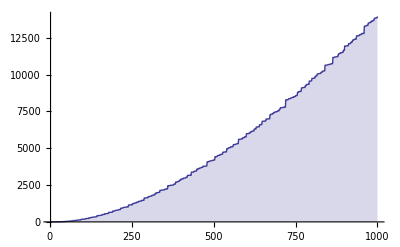

```mathematica
DiscretePlot[d4m5[x],{x,2,1000}]
```

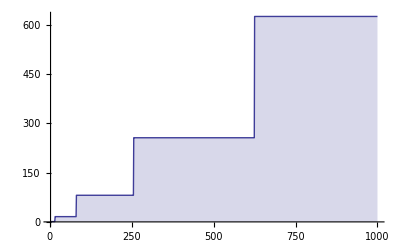

```mathematica
DDD[x_] := Floor[x^(1/4)]^4
DiscretePlot[DDD[x],{x,2,1000}]
```

```mathematica
FFF[x_ ] := Sum[4(Floor[x/(u^3)]+Floor[Floor[x/u]^(1/3)]^3),{u, 2, x^(1/4)}]
```

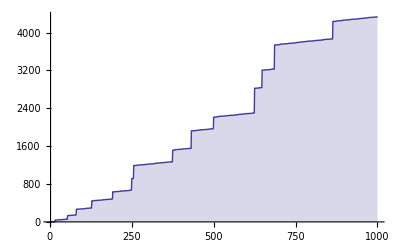

```mathematica
DiscretePlot[ FFF[x],{x,2,1000}]
```

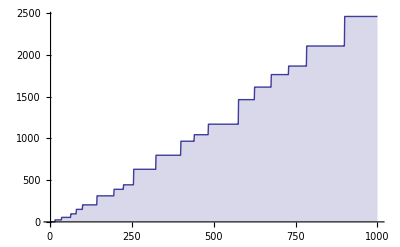

```mathematica
GGG[x_ ] := Sum[6 Floor[ Floor[x/(u^2)]^(1/2)]^2,{u, 2, x^(1/4)}]
DiscretePlot[GGG[x],{x,2,1000}]
```

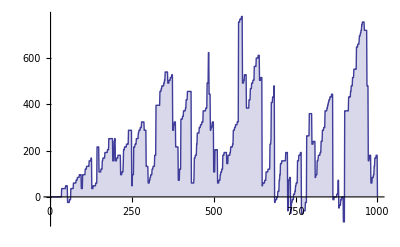

```mathematica
HHH[x_] := Sum[12 (Sum [  Floor[x/(u^2 s)], {s,(u+1),Floor[Floor[x/(u^2)]^(1/2)]}]+
Sum[ Floor[x/( u s^2)]-Floor[Floor[x/(u s)]^(1/2)]^2,{s,(u+1),Floor[Floor[x/u]^(1/3)]}]),{u, 2, x^(1/4)}]
DiscretePlot[HHH[x],{x,2,1000}]
```

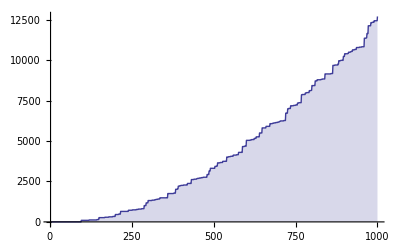

```mathematica
III[x_] := Sum[24  Sum[  Floor[x/(u m s)],{s,u+1,(x/u)^(1/3)},{m,s+1,(x/(u s))^(1/2)}],{u, 2, x^(1/4)}]
DiscretePlot[III[x],{x,2,1000}]
```

```mathematica
JJJ[x_] := 1-DDD[x]+FFF[x]-GGG[x]+HHH[x]+III[x]

DiscretePlot[JJJ[x],{x,2,1000}]
```

-Graphics-

```mathematica
DH[n_,k_,s_]:=Sum[Binomial[k,k-j] DH[n/m^j,k-j,m+1],{m,s,n^(1/k)},{j,1,k}]
DH[n_,0,s_]:=1
```

```mathematica
DH[100,2,1]
```

482

```mathematica
Sum[2 DH[100/m,1,m+1]+1,{m,1,100^(1/2)}]
```

482

```mathematica
Sum[2 (Floor[100/m]-m)+1,{m,1,100^(1/2)}]
```

482

```mathematica
Floor[100^(1/2)]+Sum[2 Floor[100/m]-2 m,{m,1,100^(1/2)}]
```

482

```mathematica
Floor[100^(1/2)]-2( Floor[100^(1/2)] (Floor[100^(1/2)]+1))/2+Sum[2 Floor[100/m],{m,1,100^(1/2)}]
```

482

```mathematica
DP[n_] := Floor[n^(1/2)]-2 (Floor[n^(1/2)] (Floor[n^(1/2)]+1))/2+Sum[2 Floor[n/m],{m,1,n^(1/2)}]
```

```mathematica
DP[100]
```

482

```mathematica
Expand[Floor[n^(1/2)]-2 (Floor[n^(1/2)] (Floor[n^(1/2)]+1))/2]
```

-Floor[√n]^2

```mathematica
DH[n_,k_,s_]:=Sum[Sum[Binomial[k,k-j] DH[Floor[n/m^j],k-j,m+1],{m,s,n^(1/k)}],{j,1,k}]
```

```mathematica
DH[n,2,s]
```

1+√n-s+∑_(m=s)^(√n) 2 (-m+Floor[n/m])

```mathematica
DH[n,1,s]
```

1+n-s

```mathematica
DH[n,3,1]
```

$Aborted

```mathematica
DH[n,2,s] := 1+√n-s+∑_(m=s)^(√n) 2 (-m+Floor[n/m])
```

```mathematica
DH[n,1,s] := 1+n-s
```

```mathematica
DH[n,3,s]
```

$Aborted